## 数字

## 罗马数字

```mathematica
FromRomanNumeral/@{"MDCCCVII","MDCCCLXXIV"}//("埃兹拉·康奈尔（Ezra Cornell，"<>ToString@#[[1]]<>"-"<>ToString@#[[2]]<>"）"&)
```

埃兹拉·康奈尔（Ezra Cornell，1807-1874）

## 牛顿分形

代码参考：https://mathematica.stackexchange.com/questions/100053/my-introduction-to-compile/100055#100055

科普视频：https://www.youtube.com/watch?v=-RdOwhmqP5s

```mathematica
(*牛顿迭代法求z^n-1=0的根，z为迭代起点，maxIterations为最大迭代次数，返回归一化幅值*)
newtonFractalCompiled=Compile[{{n,_Integer},{z,_Complex},{maxIterations,_Integer}},Arg[FixedPoint[#-(#^n-1)/(n #^(n-1))&,N[z],maxIterations]]/(2 Pi)]
```

CompiledFunction[…]

### 改变迭代次数

```mathematica
DensityPlot[newtonFractalCompiled[3,x+I y,#],{x,-2,2},{y,-2,2},PlotPoints->300,ColorFunction->"DeepSeaColors"]&/@{1,2,5,10}//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

### 改变方程次数

时不产生分形

```mathematica
DensityPlot[newtonFractalCompiled[#,x+I y,50],{x,-2,2},{y,-2,2},PlotPoints->300,ColorFunction->"DeepSeaColors"]&/@{2,3,4,5}//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

上图中的任一点，要么收敛到某个根，要么可以到达所有根
设方程有  个根，在图中画半径任意小的圆，要么只包含一种颜色，要么同时包含  种颜色，这就是分形的来源

## Britney Gallivan 折纸公式

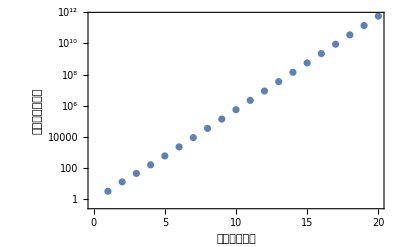

```mathematica
ListLogPlot[Table[{n,Pi/6(2^n+4)(2^n-1)},{n,1,20}],PlotTheme->"Detailed",FrameLabel->{"最大折叠次数","纸条长度厚度比"}]
```